```mathematica
(*Double well potential*)
```

```mathematica
v[x_]:=-x^2/2+x^4/24;
```

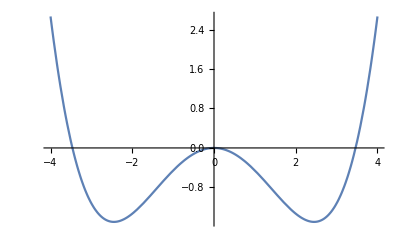

```mathematica
Plot[v[x],{x,-4,4}]
```

```mathematica
xMax=6;
```

```mathematica
(*ground state energy*)
```

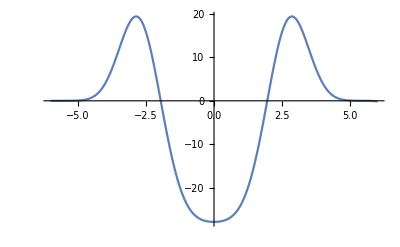

```mathematica
energy=0.07160236;
solution=NDSolve[{psi''[x]==-2(energy-v[x])psi[x], psi[-xMax]==0, psi'[-xMax]==0.001},psi,{x,-xMax, xMax}];
Plot[psi[x]/. solution,{x,-xMax,xMax}]
```

```mathematica
(*First excited state energy*)
```

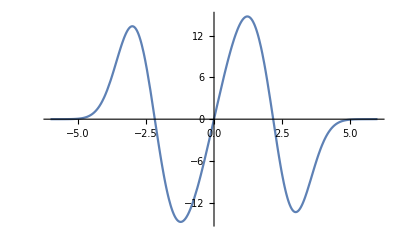

```mathematica
energy=0.45157662;
solution=NDSolve[{psi''[x]==-2(energy-v[x])psi[x], psi[-xMax]==0, psi'[-xMax]==0.001},psi,{x,-xMax, xMax}];
Plot[psi[x]/. solution,{x,-xMax,xMax}]
```